### Definitions

```mathematica
Np =4;
d = 1;
lm = 1;
lp[k_]:=((k+1)^(-1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
```

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

### Coefficients from Analytical Calculation

```mathematica
d1616[a_,b_]:=(6*(a-3 b)^(3/2))/(3 (a-2 b) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));
int1212[a_,b_]:=4*(4 a^(5/2) (a-3 b)^(3/2) (4 a^4-32 a^3 b+94 a^2 b^2-120 a b^3+57 b^4))/(√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) (4 a^2-16 a b+15 b^2)^2 √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));
```

```mathematica
int1213[a_,b_]:=0;
int1313[a_,b_]:=(4*4 a^(3/2) (a-3 b)^(3/2) (a-2 b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))/(√(a-b) (a^2-3 a b+2 b^2) ((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2))^(3/2) ((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));
```

```mathematica
int1414[a_,b_]:=4*(4 a^(5/2) (a-3 b)^(3/2) (4 a^4-32 a^3 b+94 a^2 b^2-120 a b^3+57 b^4))/(√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) (4 a^2-16 a b+15 b^2)^2 √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));
int1415[a_,b_]:=0;
int1515[a_,b_]:=(4*4 a^(3/2) (a-3 b)^(3/2) (a-2 b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))/(√(a-b) (a^2-3 a b+2 b^2) ((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2))^(3/2) ((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));
```

```mathematica
int88[a_,b_]:=6*(a^2 (16 a^8-256 a^7 b+1724 a^6 b^2-6352 a^5 b^3+13957 a^4 b^4-18728 a^3 b^5+15096 a^2 b^6-6816 a b^7+1464 b^8))/(48 (a-3 b)^(5/2) √((a (a-2 b))/(a-b)) (a-b)^(9/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
(*int1111[a_,b_]:=6*-((√((a (a-2 b))/(a-b)) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-8 a^6+96 a^5 b-456 a^4 b^2+1088 a^3 b^3-1377 a^2 b^4+900 a b^5-258 b^6))/(24 a^2 (a-3 b)^(5/2) (a-b)^(7/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a))));*)
int1111[a_,b_]:=-6((a^2 (-4 a^4+32 a^3 b-93 a^2 b^2+116 a b^3-54 b^4))/(12 √(a-3 b) √((a (a-2 b))/(a-b)) (a-b)^(5/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a))))
```

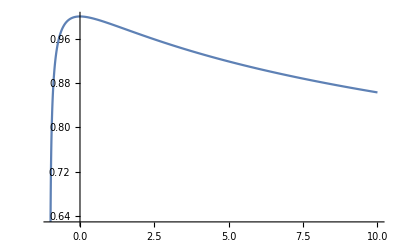

```mathematica
Plot[int88[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,10}]
```

```mathematica
int23[a_,b_]:=0;
int45[a_,b_]:=0;
int33[a_,b_]:=(4 √a (2 a^2-8 a b+5 b^2))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2) √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)));
int55[a_,b_]:=(4 √a (2 a^2-8 a b+5 b^2))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2) √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)));
int22[a_,b_]:=(4 √a (8 a^4-64 a^3 b+152 a^2 b^2-96 a b^3+31 b^4))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^2 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)));
int44[a_,b_]:=(4 √a (8 a^4-64 a^3 b+152 a^2 b^2-96 a b^3+31 b^4))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^2 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)));
int811[a_,b_]:=6*((a √((a (a-2 b))/(a-b)) b^3 (a^2-4 a b+8 b^2))/(8 (a-3 b)^(3/2) (a-b)^(5/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a))));
int66[a_,b_]:=6*(a^2 (a-3 b)^(3/2))/(3 √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));
int77[a_,b_]:=6*(a^2 (a-3 b)^(3/2))/(3 √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));
```

```mathematica
int99[a_,b_]:=-6*((√((a (a-2 b))/(a-b)) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-8 a^6+96 a^5 b-456 a^4 b^2+1088 a^3 b^3-1377 a^2 b^4+900 a b^5-258 b^6))/(24 a^2 (a-3 b)^(5/2) (a-b)^(7/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a))));

int1010[a_,b_]:=-6*((√((a (a-2 b))/(a-b)) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-8 a^6+96 a^5 b-456 a^4 b^2+1088 a^3 b^3-1377 a^2 b^4+900 a b^5-258 b^6))/(24 a^2 (a-3 b)^(5/2) (a-b)^(7/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a))));
```

```mathematica
int89[a_,b_]:=0
int810[a_,b_]:=0
int910[a_,b_]:=0
int911[a_,b_]:=0
int1011[a_,b_]:=0
```

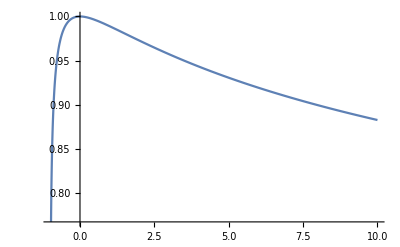

```mathematica
Plot[int99[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,10}]
```

### Define Proper Matrix Elements and MatrixForm

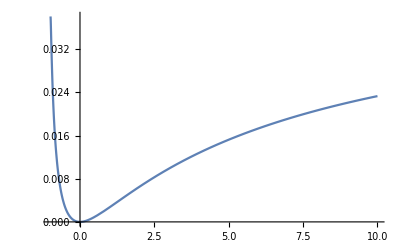

```mathematica
(*for N=3 sector*)
d1515[a_,b_]:=int1515[a,b]-d1616[a,b]
d1414[a_,b_]:=int1414[a,b]-d1616[a,b]
d1313[a_,b_]:=int1313[a,b]-d1616[a,b]
d1212[a_,b_]:=int1212[a,b]-d1616[a,b]
od1415[a_,b_]:=-int1415[a,b]
od1213[a_,b_]:=int1213[a,b]



Plot[d1313[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,10}]
threematrix[a_,b_]:={{d1212[a,b],od1213[a,b],0,0},{od1213[a,b],d1313[a,b],0,0}, {0,0,d1414[a,b],od1415[a,b]}, {0,0,od1415[a,b], d1515[a,b]}}
```

```mathematica
Eigenvalues[threematrix[A[lp[10.1]], B[lm,lp[10.1],Np]]]
```

{0.0234222,0.0234222,0.00860409,0.00860409}

```mathematica
(*for N=2 sector *)
d1111[a_,b_]:=int1111[a,b]-d1313[a,b]-d1515[a,b]-d1616[a,b];
d1010[a_,b_]:= int1010[a,b]-d1313[a,b]-d1414[a,b]-d1616[a,b];
d99[a_,b_]:=int99[a,b]-d1212[a,b]-d1515[a,b]-d1616[a,b];
d88[a_,b_]:= int88[a,b]-d1212[a,b]-d1414[a,b]-d1616[a,b];
d77[a_,b_]:=int77[a,b]-d1414[a,b]-d1515[a,b]-d1616[a,b];
d66[a_,b_]:=int66[a,b]-d1212[a,b]-d1313[a,b]-d1616[a,b];
od89[a_,b_]:=int89[a,b]-od1415[a,b]
od810[a_,b_]:=int810[a,b]-od1213[a,b]
od811[a_,b_]:=int811[a,b]
od910[a_,b_]:=int910[a,b]
od911[a_,b_]:=int911[a,b]-od1415[a,b]
od1011[a_,b_]:=int1011[a,b]-od1213[a,b]
```

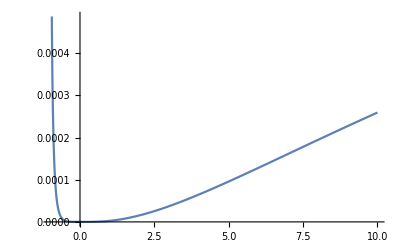

```mathematica
Plot[d77[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,10}]
```

```mathematica
twomatrix[a_,b_]:={{d66[a,b],0,0,0,0,0},{0,d77[a,b],0,0,0,0},{0,0,d88[a,b],od89[a,b],od810[a,b],od811[a,b]},{0,0,od89[a,b],d99[a,b],od910[a,b],od911[a,b]},{0,0,od810[a,b],od910[a,b],d1010[a,b],od1011[a,b]},{0,0,od811[a,b],od911[a,b],od1011[a,b],d1111[a,b]}}
```

```mathematica
Eigenvalues[twomatrix[A[lp[10.1]], B[lm,lp[10.1],Np]]]
```

{0.0763063,0.00704788,0.00704788,0.000555071,0.000262651,0.000262651}

```mathematica
(*N=1 sector*)
d55[a_,b_]:=int55[a,b]-d77[a,b]-d1010[a,b]-d1111[a,b]-d1313[a,b]-d1414[a,b]-d1515[a,b]-d1616[a,b]
d44[a_,b_]:=int44[a,b]-d77[a,b]-d88[a,b]-d99[a,b]-d1212[a,b]-d1414[a,b]-d1515[a,b]-d1616[a,b]
d33[a_,b_]:=int33[a,b]-d66[a,b]-d99[a,b]-d1111[a,b]-d1212[a,b]-d1313[a,b]-d1515[a,b]-d1616[a,b]
d22[a_,b_]:=int22[a,b]-d66[a,b]-d1010[a,b]-d88[a,b]-d1313[a,b]-d1212[a,b]-d1414[a,b]-d1616[a,b]
od45[a_,b_]:=-int45[a,b]+int89[a,b]+int911[a,b]-int1415[a,b]
od23[a_,b_]:=-int23[a,b]+int810[a,b]+int911[a,b]-int1213[a,b]
onematrix[a_,b_]:={{d22[a,b], od23[a,b],0,0},{od23[a,b], d33[a,b],0,0},{0,0,d44[a,b], od45[a,b]},{0,0,od45[a,b], d55[a,b]}}
```

```mathematica
Eigenvalues[onematrix[A[lp[10.1]], B[lm,lp[10.1],Np]]]
```

{0.000567712,0.000567712,0.000252336,0.000252336}

```mathematica
vac[a_,b_]:=1-d22[a,b]-d33[a,b]-d44[a,b]-d55[a,b]-d66[a,b]-d77[a,b]-d88[a,b]-d99[a,b]-d1010[a,b]-d1111[a,b]-d1212[a,b]-d1313[a,b]-d1414[a,b]-d1515[a,b]-d1616[a,b]
```

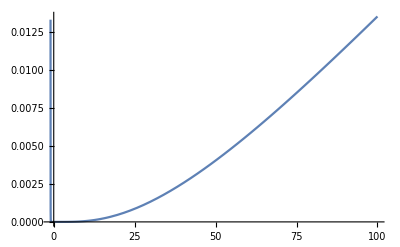

```mathematica
Plot[vac[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,100}]
```

```mathematica
fullmatrix[k_]:=Fold[ArrayFlatten[{{#,0},{0,#2}}]&,vac[A[lp[k]], B[lm,lp[k],Np]],{onematrix[A[lp[k]], B[lm,lp[k],Np]],twomatrix[A[lp[k]], B[lm,lp[k],Np]],threematrix[A[lp[k]], B[lm,lp[k],Np]], d1616[A[lp[k]], B[lm,lp[k],Np]]}]
```

```mathematica
Eigenvalues[fullmatrix[-0.99]]
```

{0.57496,0.171133,0.0395209,0.0395209,0.0380672,0.0380672,0.0157788,0.0157788,0.0133416,0.0110107,0.0110107,0.0106912,0.0106912,0.00784546,0.0012915,0.0012915}

```mathematica
fullmatrix[-0.99] //MatrixForm
```

(0.0133416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0110107 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0106912 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0110107 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0106912 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0012915 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.0012915 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0225782 | 0 | 0 | -0.0467827 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0395209 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0395209 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0467827 | 0 | 0 | 0.1564 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0157788 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0380672 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0157788 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0380672 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.57496)

### Calculating Entanglement Measures

```mathematica
(*s[i_]:=If[i==0,0,-i*Log[i]]

p8[a_,b_]:=d99[a,b]
p9[a_,b_]:=d1010[a,b]
p10[a_,b_]:=d66[a,b]
p11[a_,b_]:=d77[a,b]

p1[a_,b_]:= vac[a,b]
p2[a_,b_]:= d88[a,b]
p3[a_,b_]:= d1111[a,b]
p4[a_,b_]:=d1616[a,b]

sp[a_,b_]:= p8[a,b]+p9[a,b]+p10[a,b]+p11[a,b]
ap[a_,b_]:=sp[a,b]^2-(p10[a,b]-p11[a,b])^2
bp[a_,b_]:=(Abs[p8[a,b]-p9[a,b]])*sp[a,b]
cp[a_,b_]:=(p10[a,b]+p11[a,b])^2*(Abs[p8[a,b]-p9[a,b]])^2+8*p10[a,b]*p11[a,b](2*p10[a,b]*p11[a,b]+(p10[a,b]+p11[a,b])(p8[a,b]+p9[a,b])+2*p8[a,b]*p9[a,b])
q8[a_,b_]:= If[p8[a,b]>p9[a,b],(ap[a,b]+bp[a,b]+Sqrt[cp[a,b]])/(4*sp[a,b]-p9[a,b]), (ap[a,b]+bp[a,b]+Sqrt[cp[a,b]])/(4*sp[a,b]-p8[a,b])]
q9[a_,b_]:= If[p8[a,b]>p9[a,b],(ap[a,b]-bp[a,b]-Sqrt[cp[a,b]])/((4*sp[a,b]-p8[a,b])), (ap[a,b]-bp[a,b]-Sqrt[cp[a,b]])/((4*sp[a,b]-p9[a,b]))]
q10[a_,b_]:= p10[a,b]+(p8[a,b]+p9[a,b]-q8[a,b]-q9[a,b])/(2)
q11[a_,b_]:= p11[a,b]+(p8[a,b]+p9[a,b]-q8[a,b]-q9[a,b])/(2)

spp[a_,b_]:= p2[a,b]+p3[a,b]+p1[a,b]+p4[a,b]
app[a_,b_]:=spp[a,b]^2-(p1[a,b]-p4[a,b])^2
bpp[a_,b_]:=(Abs[p2[a,b]-p3[a,b]])*spp[a,b]
cpp[a_,b_]:=(p1[a,b]+p4[a,b])^2*(Abs[p2[a,b]-p3[a,b]])^2+8*p1[a,b]*p4[a,b](2*p1[a,b]*p4[a,b]+(p1[a,b]+p4[a,b])(p2[a,b]+p3[a,b])+2*p2[a,b]*p3[a,b])
q2[a_,b_]:= If[p2[a,b]>p3[a,b],(app[a,b]+bpp[a,b]+Sqrt[cpp[a,b]])/(4*spp[a,b]-p3[a,b]), (app[a,b]+bpp[a,b]+Sqrt[cpp[a,b]])/(4*spp[a,b]-p2[a,b])]
q3[a_,b_]:= If[p2[a,b]>p3[a,b],(app[a,b]-bpp[a,b]-Sqrt[cpp[a,b]])/((4*spp[a,b]-p2[a,b])), (app[a,b]-bpp[a,b]-Sqrt[cpp[a,b]])/((4*spp[a,b]-p3[a,b]))]
q1[a_,b_]:= p1[a,b]+(p2[a,b]+p3[a,b]-q2[a,b]-q3[a,b])/(2)
q4[a_,b_]:= p4[a,b]+(p2[a,b]+p3[a,b]-q2[a,b]-q3[a,b])/(2)

enssr[a_,b_]:=s[q8[a,b]]+s[q9[a,b]]+s[q10[a,b]]+s[q11[a,b]]
epssr[a_,b_]:=enssr[a,b]+(s[q1[a,b]]+s[q2[a,b]]+s[q3[a,b]]+s[q4[a,b]])*)
```

```mathematica
matrixEP[k_]:={{d66[A[lp[k]], B[lm,lp[k],Np]],0,0,0},{0,d77[A[lp[k]], B[lm,lp[k],Np]],0,0},{0,0,d99[A[lp[k]], B[lm,lp[k],Np]],od910[A[lp[k]], B[lm,lp[k],Np]]},{0,0,od910[A[lp[k]], B[lm,lp[k],Np]],d1010[A[lp[k]], B[lm,lp[k],Np]]}}
matrixEN[k_]:={{vac[A[lp[k]], B[lm,lp[k],Np]],0,0,0},{0,d88[A[lp[k]], B[lm,lp[k],Np]],od811[A[lp[k]], B[lm,lp[k],Np]],0},{0,od811[A[lp[k]], B[lm,lp[k],Np]],d1111[A[lp[k]], B[lm,lp[k],Np]],0},{0,0,0,d1616[A[lp[k]], B[lm,lp[k],Np]]}}
```

```mathematica
matexportfunct[i_, ind_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/"<>"data_m01_negk"<>ToString[ind]<>".mat", fullmatrix[i]]
matexportfunctEP[i_, ind_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01dataEP/"<>"data_m01EP_k"<>ToString[ind]<>".mat", matrixEP[i]]
matexportfunctEN[i_, ind_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01dataEN/"<>"data_m01EN_k"<>ToString[ind]<>".mat", matrixEN[i]]

kappalogrange[i_]:= If[i≤1, i, 10^(i-1)]
kappamin = -0.99;
kappamax = 0;
kappagran = 0.05;
kappalist = Table[kappalogrange[k], {k,kappamin, kappamax, kappagran}];
Table[matexportfunct[kappalist[[i]],i],{i,1,Length[kappalist]}]
(*Table[matexportfunctEN[kappalist[[i]],i],{i,1,Length[kappalist]}]*)
```

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk1.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk2.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk3.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk4.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk5.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk6.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk7.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk8.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk9.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk10.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk11.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk12.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk13.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk14.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk15.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk16.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk17.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk18.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk19.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Fermions Analytic Results/Analytic Results spinN4d1_1mode/mode-mode-ent/matlab_m01data/data_m01_negk20.mat}

```mathematica
(*without SSR*)
e[k_, i_] := s[q0[k][[i+1]]]+s[q1[k][[i+1]]]+s[q2[k][[i+1]]]+s[q3[k][[i+1]]]
i[k_,i_]:= 2*e[k,i]
(*with PSSR*)
ip[k_, m_] := 2*e[k,m]-s[(q0[k][[m+1]]+q3[k][[m+1]])] -s[(q1[k][[m+1]]+q2[k][[m+1]])]
ep[k_, m_] := e[k,m]-s[(q1[k][[m+1]]+q2[k][[m+1]])]-s[(q0[k][[m+1]]+q3[k][[m+1]])]
(*with NSSR*)
in[k_, m_] := 2*e[k,m]-s[q0[k][[m+1]]]-s[(q1[k][[m+1]]+q2[k][[m+1]])]-s[q3[k][[m+1]]]
en[k_, m_] := -s[(q1[k][[m+1]]+q2[k][[m+1]])]+s[ q1[k][[m+1]]]+s[q2[k][[m+1]]]
```

```mathematica
export[dataset_,label_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/data_ferm_4d1_mode/"<>ToString[label],dataset, "CSV"]
```

```mathematica
(*export[Flatten[Table[ip[k,2], {k,-0.99,-0.01,0.01}]], ipmode2neg]*)
```

```mathematica
"/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/data_ferm_4d1_mode/ipmode2neg"
```

/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/data_ferm_4d1_mode/ipmode2neg

```mathematica
kappalogrange[i_]:= If[i≤0, i, 10^(i-1)]
(*epeexpneg[i_]:=export[Flatten[Table[ep[k,i]/e[k,i], {k,-0.99,-0.01,0.01}]], "epemode"<>ToString[i]"neg"]
eneexpneg[i_]:=export[Flatten[Table[en[k,i]/e[k,i], {k,-0.99,-0.01,0.01}]], "enemode"<>ToString[i]"neg"]
epeexppos[i_]:=export[Flatten[Table[ep[kappalogrange[k],i]/e[kappalogrange[k],i], {k,0.01,5,0.01}]], "epemode"<>ToString[i]"pos"]
eneexppos[i_]:=export[Flatten[Table[en[kappalogrange[k],i]/e[kappalogrange[k],i], {k,0.01,5,0.01}]], "enemode"<>ToString[i]"pos"]*)
```